```mathematica
Ez=0.9*wc;
```

```mathematica
data={};
For[Ez=0,Ez≤0.8*wc,Ez+=0.01,
{
```

```mathematica
Clear[wc,w,μ,nn,me,wp,x];
μ=50;
nn=0;
wc=μ/(nn+3/2);
(*Ez=(3/4)*wc;*)
{V0,me,α}={1,1,0.0};
ϵ[n_,s_]:=(n+1)*wc-Sign[s]*0.5*Sqrt[(Ez-wc)^2];
μ=0.5*(ϵ[nn+1,+1]+ϵ[nn,-1]);
δϵ[n_]:=ϵ[n,-1]-ϵ[n,+1];
θ[n_]:=ArcCos[(Ez-wc)/δϵ[n]];
kf[n_,s_]:=Piecewise[{{Sqrt[2*me*μ-2*me*(n+1/2)*wc+me*Ez],s==1&&0≤n≤(nn+1)},{ Sqrt[2*me*μ-2*me*(n+1/2)*wc-me*Ez],s==-1&&0≤n≤nn}},0];
KF=Table[kf[n,s],{n,0,nn+1},{s,-1,+1,2}];
l=1/Sqrt[me*wc];
sf[m_,n_,p_]:=-(1/Pi)*(1/l)*P1[[m+1,n+1]]*KF[[n+1,p]];
Σ[m_,p_]:=Sum[sf[m,n,p],{n,0,nn+1}];
pi[n_,m_]:=Piecewise[{{(1/Pi)*(KF[[m+2,2]]-KF[[m+1,2]])/(Σ[m+1,2]-Σ[m,2]-wc+w),n==m},{0,n≠m}}];
v[n_,m_]:=(1/l)*P2[[n+1,m+1]];
Π=Table[pi[n,m],{n,0,nn},{m,0,nn}];
Σmatrix=Table[Σ[n,p],{n,0,nn+1},{p,1,2}];s[n_,m_]:=Piecewise[{{(-1)*(Σmatrix[[n+1,2]]-Σmatrix[[n+2,2]]),n==m&&n≤nn}},0];
smatrix=Table[s[n,m],{n,0,nn},{m,0,nn}];(*\CapitalSigmamatrix[[**,1->2*)vmatrix=Table[v[n,m],{n,0,nn},{m,0,nn}];
k[n_,m_]:=Piecewise[{{(1/Pi)*(KF[[n+2,1]]-KF[[n+1,1]]),n==m&&n≤nn}},0];
kmatrix=Table[k[n,m],{n,0,nn},{m,0,nn}];
M=-kmatrix.vmatrix-smatrix;
```

```mathematica
V0=1;
mm=Eigenvalues[M][[nn+1]];
ω=V0*mm+δϵ[0];
AppendTo[data,{Ez/wc,ω/wc}];}]
```

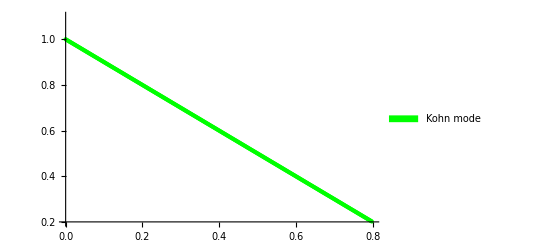

```mathematica
f3=ListPlot[data,PlotRange->{{0,0.8},{0.2,1.1}},PlotStyle->Green,PlotLegends->SwatchLegend[{Green},{"Kohn mode"}]]
```

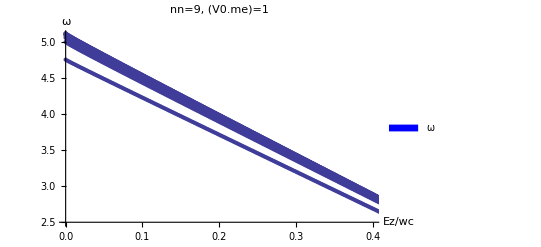

```mathematica
f1=ListPlot[data,AxesLabel->{"Ez/wc","ω"},PlotLabel->"nn=9, (V0.me)=1",PlotRange->{{0,0.4},{2.5,5.1}},PlotLegends->SwatchLegend[{Blue},{"ω"}]]
```

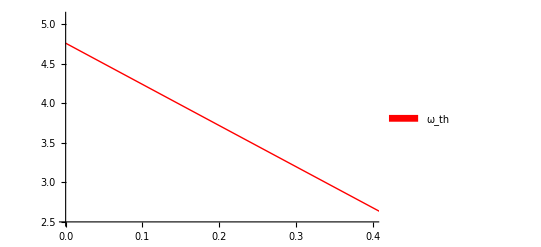

```mathematica
Clear[Ez];f2=Plot[-((p)*wc*(1+V0/(4*Pi-2*me*V0))-Sqrt[(V0*(p)*wc*me/(4*Pi-2*me*V0))^2+wc^2]),{p,0,2},PlotRange->{{0,0.4},{2.5,5.1}},PlotStyle->Red,PlotLegends->SwatchLegend[{Red},{"ω_th"}]]
```

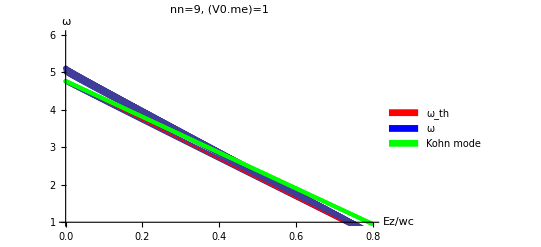

```mathematica
Show[f1,f2,f3]
```

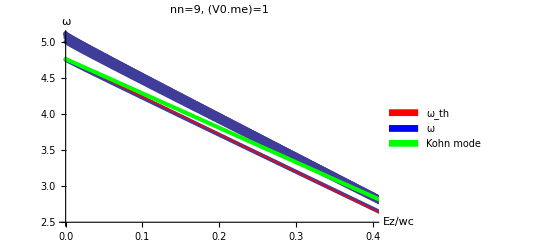

```mathematica
Show[f1,f2,f3]
```